# Homogeneous 1st order linear differential equation

```mathematica
ClearAll["Global`*"];
```

## Homogeneous 1st order linear differential equation with constant coefficients and initial conditions

```mathematica
equation=y'[t]-y[t]==0;
```

```mathematica
initialCondition=y[0]==1;
```

```mathematica
sol=First@DSolve[{equation,initialCondition},y[t],t];
```

```mathematica
y=y[t]/.sol
```

ⅇ^t

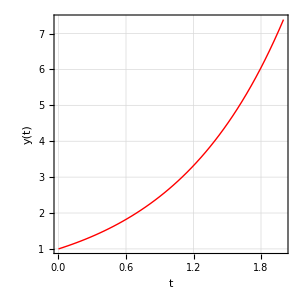

```mathematica
Plot[y,{t,0,2},
FrameLabel->{{"y(t)",None},{"t","Solution"}},
Frame->True,
GridLines->Automatic,
GridLinesStyle->Automatic,
RotateLabel->True,
PlotRange->All,
AspectRatio->1,
PlotStyle->{Thick,Red}]
```